# Late-Time Phenomenology For A General Scalar-Tensor Model.

## Canonical Scalar Field Non-Minimally Coupled To Ricci Scalar And Gauss-Bonnet Topological Invariant.

Hereafter, MP is the Planck mass, ms is a mass scale related to κ^2ρ0 with ρ0 being the current density of dust, χ is the current density of radiation over dust, M is a different Mass scale, each function/parameter ending with “dot” implies derivative with respect to cosmic time t hence it is rewritten appropriately as a derivative of redshift z, X is the kinetic term of the scalar field while V is the scalar potential, ρ is the sum of dust and radiation density, R0 is the real/proper Ricci scalar which is replaced in the f(R,Φ) function after calculations (for instance derivatives) have been carried, similar for Φ and H2 stands for Hubble squared, it is easy to remember. YH is the function that we find as solution to the equations of motion instead of Hubble however yH is the proper statefinder we focus on, which is assigned the function satisfying the equations of motion, similar for the scalar field. Moreover, functions with the number 1 are similarly functions of the proper yH and φ solutions and facilitate us into extracting results for the statefinders. Referring to statefinders, q is as usual the deceleration parameter, j is the jerk and s is the snap, all of them connected with derivates of Hubble, however must be written with respect to redshift. Om is an extra statefinder for which mainly the current value matters, as it must coincide or actually be quite close to the current value of the matter density parameter Ωm. Finally, functions ending with DE are related to dark energy, meaning all the extra geometric terms appearing in the equations of motion. In particular, ωDE stands for the Equations of state (EoS) parameter whereas ΩDE  as before signifies the Dark Energy density parameter. 

ΛCDM Values: Roughly speaking, q near -0.535, j near unity, snap near 0, Om near 0.315, ωDE near -1 (does not have to be exactly -1, it can also vary infinitesimally as shown in this particular model) and ΩDE near 0.685 such stat Om+ΩDE near unity (Friedman constraint). More details+accurate values can be found in arXiv: 1807.06209.

Fun fact, f(R) gravity is known for producing dark energy oscillations for large values of redshift, exactly as shown in section 3. Higher derivatives of Hubble (or for consistency yH) imply faster oscillations as shown in the jerk and snap. Adding a simple canonical kinetic term does not nullify them. The non-minimal coupling here was neglected along with the scalar potential and the Gauss-Bonnet scalar coupling function ξ(φ) for simplicity, the user however is capable of adding even more scalar terms, for instance a k-essence term or a noncanonical kinetic term (perhaps a Born-Infeld term). In particular, for this f(R) model, given that R^(1/100) becomes dominant as z approaches zero (since R->0 as well) the “singularity” which appears in the equations of motion is too difficult to overcome so a plethora of models, and perhaps with different free parameters, may yield the same results. As an example, see the following two arXiv papers.

## 1. Designation Of Model.

### 1.1. Assigning Values To The Free Parameters.

Suppose we have a similar f(R) model as in arXiv:1912.13128 and arXiv:2003.06671 such that early-late time is unified, where now a canonical scalar field with an arbitrary and not necessarily quadratic scalar potential is also present. In order to solve numerically the equations of motion in the area [-0.9,10] for redshift, one needs to specify the initial conditions, here denoted with 0 in the end and D in front for derivatives, given that we have second order derivatives for both Hubble and the scalar field participating in the equations of motion. Initial conditions for statefinder yH are taken from observations so they should not alter. In contrast, other parameters of the model, along with the initial conditions of the scalar field (since it is not observed) can be freely altered. Pay attention to the dimensionality of each free parameter, in particular [f(R,φ)]=ev^2, [φ]=ev, [yH]=dimensionless and so on.

```mathematica
κ=1/MP;
MP=1.2 10^27;
ms=√(1.87101 10^-67);
Λ=11.895 10^-67;
Y0=Λ/(3 ms^2)(1+11/1000);
DY0=Λ/(3000 ms^2);
χ=3.1 10^-4;
Φ0=10^-16 MP;
DΦ0=-10^-17 MP;
M=1.5 10^-5(5MP)/6;
α=0.;
V0=0.;
λ=0.;
ΦC=10^-18 MP;
```

### 1.2. Specifying The Scalar-Tensor Model And The Equations Of Motion.

Apart from defining the f(R,φ) function, it is also useful to rewrite time derivatives as derivatives with respect to redshift z. Also, instead of Hubble’s parameter, we focus on a new statefinder function, denoted as YH in this framework in order to facilitate our study by simplifying a bit the equations of motion which were rendered intricate due to the variable change a(t)->z. The main focus lies with input eq1 and eq2 as these differential equations shall be solved numerically in the aforementioned area for z. All functions are defined as g[x] instead of g[x_]: since in the latter case both the time response and the “accuracy” decreases, as the code will always summon the bare function and if it contains the solution of the equations of motion it will be unable to run properly, or for the same result one would need to add a lot more intermediate functions/steps. Either way, such definition works.

```mathematica
f[R,Φ]=h[Φ]R+(R/M)^2-2Λ(R/(3 ms^2))^(1/100);
fR[R,Φ]=D[f[R,Φ],R];
h[Φ]=1+α Φ/MP;
ξ[Φ]=λ Exp[-Φ/ΦC];
ξdot[z]=D[ξ[Φ],Φ]φdot[z]/.Φ->φ[z];
G0[z]=24H2[z](H2[z]-H[z](1+z)D[H[z],z]);
φdot[z]=-H[z](1+z)D[φ[z],z];
fRdot[z]=Rdot[z]D[fR[R,Φ],R]+φdot[z]D[fR[R,Φ],Φ];
V[Φ]=V0(κ Φ)^2;
X[z]=-1/2 φdot[z]^2;
ρ[z]=(1+z)^3(1+χ(1+z));
H2[z]=ms^2(YH[z]+ρ[z]);
H[z]=√H2[z];
R0[z]=12H2[z]-6H[z](1+z)D[H[z],z];
Rdot[z]=-H[z](1+z)D[R0[z],z];
eq1=(3H2[z]fR[R,Φ]-3 ms^2 ρ[z]+κ^2(X[z]-V[Φ])-24ξdot[z]H2[z]H[z]+(f[R,Φ]-fR[R,Φ]R0[z])/2+3H[z]fRdot[z])/.{R->R0[z],Φ->φ[z]};
eq2=(-H[z](1+z)D[φdot[z],z]+3H[z]φdot[z]+D[V[Φ],Φ]+D[ξ[Φ],Φ]G0[z]-D[f[R,Φ],Φ]/(2 κ^2))/.{R->R0[z],Φ->φ[z]};
```

## 2. Solving The Equations Of Motion

### 2.1. Derivation Of Statefinder yH And The Scalar Field.

Using as input the initial conditions specified in section 1, the solution is extracted. Compatibility with Planck data is achieved if the current value of the statefinder yH is actually quite close to 2.

```mathematica
sol=NDSolve[{eq1==0,eq2==0,YH[10]==Y0,YH'[10]==DY0,φ[10]==Φ0,φ'[10]==DΦ0},{YH,φ},{z,-0.9,10}]
yH[z]=YH[z]/.sol[[1]];
φ0[z]=φ[z]/.sol[[1]];
yH[z]/.z->0//N
```

Power::infy: Infinite expression 1/0^(199/100) encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

{{YH→InterpolatingFunction[…],φ→InterpolatingFunction[…]}}

2.16471

Afterwards, we assign the solutions in new functions and plot them. These will be used subsequently in order to study various statefinders and ascertain the validity of the model at hand. For ξ participating in the equations of motion, plot also G/ms^4. For this model, it would also oscillate. Furthermore, a comparison between the ΛCDM Hubble and the one extracted in this model is also available.

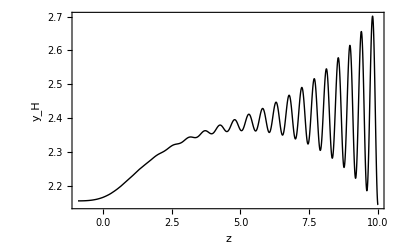

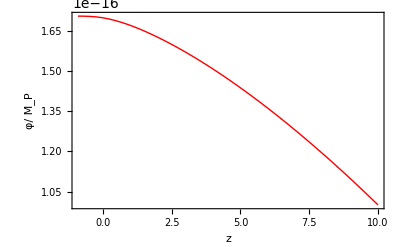

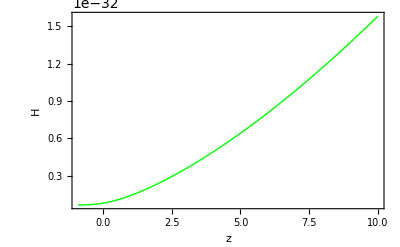

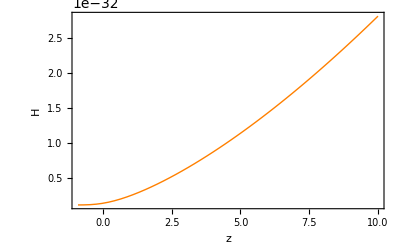

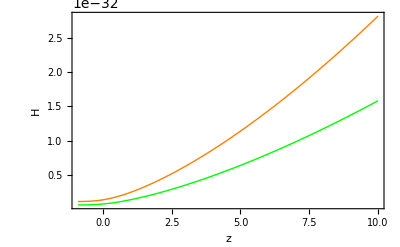

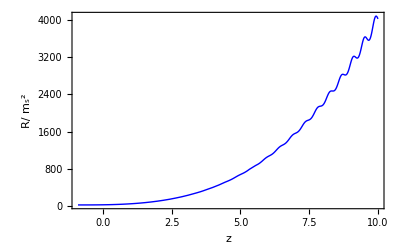

```mathematica
p1=Plot[yH[z],{z,-0.9,10},Frame->True,FrameLabel->{"z",Subscript["y","H"]},PlotRange->All,PlotStyle->Thick]
p2=Plot[φ0[z]/MP,{z,-0.9,10},Frame->True,FrameLabel->{"z", "φ/"Subscript["M","P"]},PlotRange->All,PlotStyle->{Red,Thick}]
H1[z]=ms Sqrt[yH[z]+ρ[z]];
p3=Plot[H1[z],{z,-0.9,10},Frame->True,FrameLabel->{"z","H"},PlotRange->All,PlotStyle->{Green,Thick}]
HΛCDM0=1.37187 10^-33;
ΩΛ=0.6847;
ΩM=0.3153-Ωr;
Ωr=8 10^-5;
HΛCDM[z]=HΛCDM0 Sqrt[ΩΛ+ΩM(1+z)^3+Ωr(1+z)^4];
p4=Plot[HΛCDM[z],{z,-0.9,10},Frame->True,FrameLabel->{"z","H"},PlotRange->All,PlotStyle->{Orange,Thick}]
Show[p3,p4]
R1[z]=12 H1[z]^2-6(1+z)D[H1[z],z]H1[z];
p5=Plot[R1[z]/ms^2,{z,-0.9,10},Frame->True,FrameLabel->{"z","R/"Superscript[Subscript["m","s"],2]},PlotRange->All,PlotStyle->{Blue,Thick}]
```

## 3. Statefinder Parameters.

As a final step, we study the behaviour of 6 statefinder parameters and compare results directly with data. The analysis focuses mainly on the deceleration, jerk, snap, Om(z), EoS and Density parameter of Dark Energy, all of them rewritten as functions depending solely on redshift for the sake of consistency. Above each plot, the current model predicted value of the respective statefinder is presented.

-0.520954

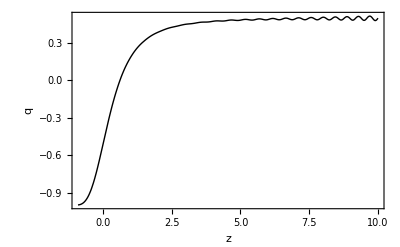

1.00319

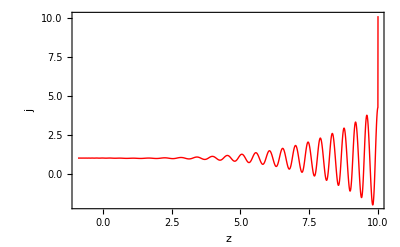

-0.00104006

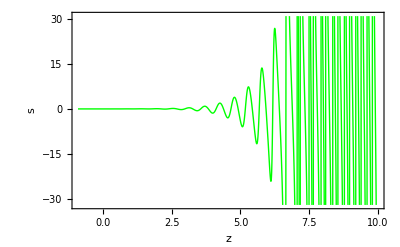

0.319364

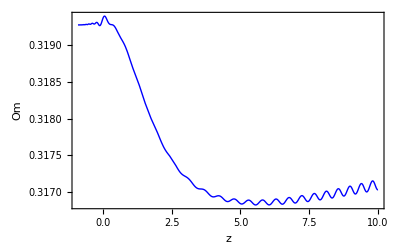

-0.995205

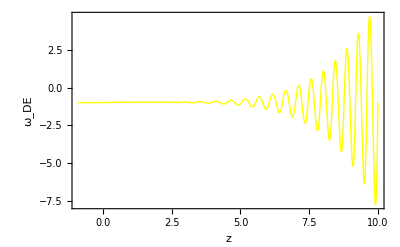

0.683948

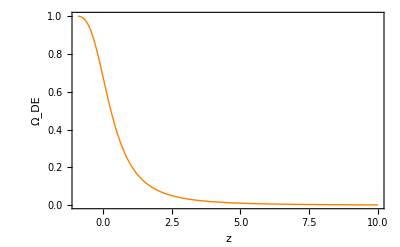

1.00331

```mathematica
q[z]=-1+(1+z)D[H1[z],z]/H1[z];
q[z]/.z->0//N
p6=Plot[q[z],{z,-0.9,10},Frame->True,FrameLabel->{"z","q"},PlotRange->All,PlotStyle->Thick]
j[z]=(1+z)D[H1[z](1+z)D[H1[z],z],z]/H1[z]^2-3q[z]-2;
j[z]/.z->0//N
p7=Plot[j[z],{z,-0.9,10},Frame->True,FrameLabel->{"z","j"},PlotRange->All,PlotStyle->{Red,Thick}]
s[z]=(j[z]-1)/(3(q[z]-1/2));
s[z]/.z->0//N
p8=Plot[s[z],{z,-0.9,10},Frame->True,FrameLabel->{"z","s"},PlotStyle->{Green,Thick}]
H10=H1[z]/.z->0;
Om[z]=((H1[z]/H10)^2-1)/((1+z)^3-1);
Om0=Om[z]/.z->10^-8//N
p9=Plot[Om[z],{z,-0.9,10},Frame->True,FrameLabel->{"z","Om"},PlotRange->All,PlotStyle->{Blue,Thick}]
ωDE[z]=-1+(1+z)/(3yH[z])D[yH[z],z];
ωDE[z]/.z->0//N
p10=Plot[ωDE[z],{z,-0.9,10}, Frame->True,FrameLabel->{"z",Subscript["ω","DE"]},PlotRange->All,PlotStyle->{Yellow,Thick}]
ΩDE[z]=yH[z]/(yH[z]+ρ[z]);
ΩDE0=ΩDE[z]/.z->0//N
p11=Plot[ΩDE[z],{z,-0.9,10}, Frame->True,FrameLabel->{"z",Subscript["Ω","DE"]},PlotRange->All,PlotStyle->{Orange,Thick}]
Om0+ΩDE0
```